```mathematica
RandomSeed[101];
(*Needs["PlotLegends`"]*)
LaTeX[x_]:=ToString[TeXForm[x]];
code[i_]:=Module[{},
kk=RandomChoice[{1/3,1/2,1,2,3}];
denom[x_]:=RandomChoice[{kk+x^2,x^2+x^3+kk,kk+x^3}];
wildFunction[x_]=RandomChoice[{Sin[x],E^Sin[x],E^Cos[x],E^ArcTan[x],2^Sin[x],2^Cos[x],2^ArcTan[x]}];
boundingFunction[x_]:=RandomChoice[{Sin[kk*x]^2,x^2,x^3*Sin[kk*x]}];

f[x_]=RandomChoice[{boundingFunction[x]*wildFunction[1/Surd[x,3]],boundingFunction[x]*wildFunction[1/Surd[x,3]],boundingFunction[x]/denom[x],boundingFunction[x]*wildFunction[1/Surd[x,3]],boundingFunction[x]*Erf[kk*x]}];
switch=Random[Integer,{1,6}];
F[x_]:=NIntegrate[f[t],{t,0,x}];
fxns[1]:={F[x],f[x],f'[x]};
fxns[2]:={F[x],f'[x],f[x]};
fxns[3]:={f[x],F[x],f'[x]};
fxns[4]:={f[x],f'[x],F[x]};
fxns[5]:={f'[x],f[x],F[x]};
fxns[6]:={f'[x],F[x],f'[x]};
(*NEED TO FIX VERIFY*)
verify[1]=If[switch==1,"[correct]",""];
verify2=If[switch==1,"","[correct]"];
graph=Plot[fxns[1],{x,-5,5},Ticks->False,PlotStyle->{{Thick,Black} ,{Thick,Black,Dashed},{Thick,Black,Dotted}},PlotLegends->{TraditionalForm[f],TraditionalForm[g],TraditionalForm[h]}];
{graph,
StringJoin["\\documentclass{ximera}
\\input{../preamble.tex}
\\author{Bart Snapp}
\\license{Creative Commons 3.0 By-NC}
\\begin{document}
\\begin{exercise}
\\outcome{Identify the relationships between the function and its first and second derivatives.}
\\tag{derivative}
Here we see a plot of $f$ and $g$. 
\\begin{image}
\\includegraphics[width=.5\\textwidth]{graphFandG",LaTeX[i],".png}
\\end{image}
Which of the following is correct?
\\begin{multipleChoice}
\\choice",verify1,"{$f'(x) = g(x)$}
\\choice",verify2,"{$g'(x) = f(x)$}
\\end{multipleChoice}
\\end{exercise}
\\end{document}"]}]
```

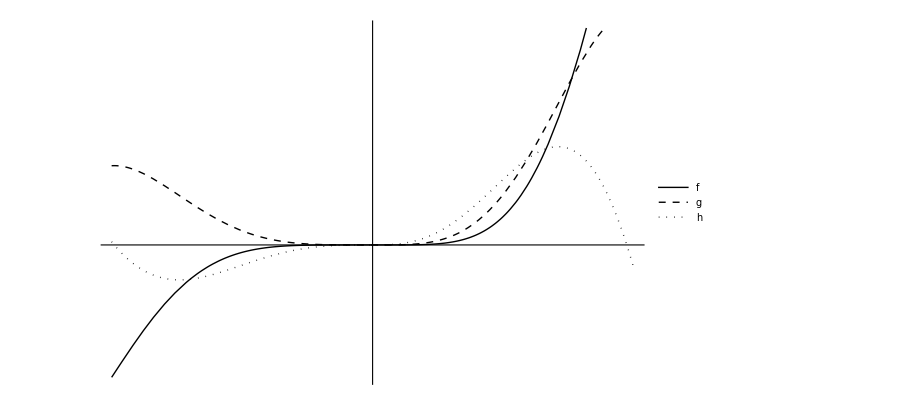
{-Graphics-,\documentclass{ximera}
\input{../preamble.tex}
\author{Bart Snapp}
\license{Creative Commons 3.0 By-NC}
\begin{document}
\begin{exercise}
\outcome{Identify the relationships between the function and its first and second derivatives.}
\tag{derivative}
Here we see a plot of $f$ and $g$. 
\begin{image}
\includegraphics[width=.5\textwidth]{graphFandG6.png}
\end{image}
Which of the following is correct?
\begin{multipleChoice}
\choice{$f'(x) = g(x)$}
\choice[correct]{$g'(x) = f(x)$}
\end{multipleChoice}
\end{exercise}
\end{document}}

```mathematica
code[6]
```

```mathematica
Do[{precode=code[i];	
Export["plotOfFxnAndDeriv"<>ToString[i]<>".tex",precode[[2]],"Text"];
Export["graphFandG"<>ToString[i]<>".png",precode[[1]],"PNG",ImageResolution->200]}
,{i,12}];
```